Supplementary Mathematica file. 
July 2017

CONTENTS: 

Part 0: “Housekeeping”, definitions of functions, matrices and replacement rules that will be used throughout the file. 

Part 1: Probabilities of identity by descent (related to Appendix B2 and C2). 
            We compare the formulas calculated by hand to the ones obtained numerically for special structures, to check that the formulas are correct (they are).
            
Part 2: Expected Frequencies Functions (related to Appendix B1 and C1, and formulas in the main text)
             - We simplify the formulas obtained by hand by replacing the dispersal (d) and interaction (e) graphs by their formulas in subdivided populations. 
             - We compare the formulas calculated by hand to the ones obtained numerically for special structures, to check that the formulas are correct (they are).
             - We export the formulas to R for further use. 

Part 3: Changes with m
             We study how the different terms of our equations (probabilities of identity by descent Q, indirect/secondary terms I, and full equations EX) change with the emigration probability m, and identify critical values.

Please note:
-  In this file, the mutation bias is denoted by p (as in Tarnita and Taylor 2014 and Debarre 2017), instead of ν as in the manuscript. 
   The letter ν was chosen in the manuscript because p was sometimes mistaken by others as average frequency of altruists in the population (X̄ in the manuscript)... But this file was written before the change, and it is too complicated to change every instance of “p”.
   
-  Make sure to change `pathtosave` with the path to the folder containing the codes.

Before doing anything, clean the memory

```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

Set path to folder where outputs should be saved (otherwise it is the default Mathematica one)

```mathematica
pathtosave="~/Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/";
```

# 0) Generalities - Initializations

## Some functions

Function to turn P (expected state of pairs of sites) into Q (probabilities of identity by descent)

```mathematica
PtoQ[P_]:=(P-p^2)/(p(1-p))//FullSimplify;
```

Delta function

```mathematica
Delta[x_]:=If[x==0,1,0]
```

## Define graphs for numerical evaluation

### Dispersal and Interaction Graphs

#### Island model, dispersal graph, generic

N = 12, 4 demes of 3 individuals

```mathematica
G12generic=({{dself, din, din, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {din, dself, din, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {din, din, dself, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, dself, din, din, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, din, dself, din, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, din, din, dself, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, dself, din, din, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, din, dself, din, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, din, din, dself, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, dself, din, din}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, din, dself, din}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, din, din, dself}});
Nin=3;
Ndemes=4;
```

N = 10, 2 demes of 5 individuals

```mathematica
G10generic=({{dself, din, din, din, din, dout, dout, dout, dout, dout}, {din, dself, din, din, din, dout, dout, dout, dout, dout}, {din, din, dself, din, din, dout, dout, dout, dout, dout}, {din, din, din, dself, din, dout, dout, dout, dout, dout}, {din, din, din, din, dself, dout, dout, dout, dout, dout}, {dout, dout, dout, dout, dout, dself, din, din, din, din}, {dout, dout, dout, dout, dout, din, dself, din, din, din}, {dout, dout, dout, dout, dout, din, din, dself, din, din}, {dout, dout, dout, dout, dout, din, din, din, dself, din}, {dout, dout, dout, dout, dout, din, din, din, din, dself}});
```

#### Island model, interaction graph, generic

```mathematica
GE12generic=G12generic/.{dself->eself,dout->eout,din->ein};
GE10generic=G10generic/.{dself->eself,dout->eout,din->ein};
```

#### Formulas for d and e

Replacements for the generic dispersal probabilities, depending on whether there is self-replacement or not

```mathematica
noselfreplacement={dself->0,din->(1-m)/(n-1),dout->m/(d n - n)};
withselfreplacement={dself->(1-m)/n,din->(1-m)/n,dout->m/(d n - n)};
```

Replacements for the generic interaction probabilities, depending on whether there is self - interaction or not

```mathematica
groupnoself={eself->0,ein->1/(n-1),eout->0};
groupwithself={eself->1/n,ein->1/n,eout->0};
```

We can even assume that there are a proportion g of interactions outside of the group

```mathematica
widewithself={eself->(1-g)/n,ein->(1-g)/n,eout->g/(n d-n)};
widenoself={eself->0,ein->(1-g)/(n-1),eout->g/(n d-n)};
```

Combine these using Idself and Ieself, indicator variables for whether there is dispersal/interaction with self

```mathematica
genericde={dself->Idself (1-m)/n,din->(1-m)(1/(n-1)-Idself 1/(n(n-1))),dout->m/(n d-n),(*
*)eself->Ieself (1-g)/n,ein->(1-g)(1/(n-1)-Ieself 1/(n(n-1))),eout->g/(n d-n)};
```

Quick check

```mathematica
eself+(n-1)ein+(n d-n)eout/.genericde//Simplify
dself+(n-1)din+(n d-n)dout/.genericde//Simplify
```

1

1

### Probabilities of identity by descent matrices

#### Generic Q matrix corresponding to the populations defined above

N = 12

```mathematica
Q12generic=({{1, Qin, Qin, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, 1, Qin, Qin, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1}});
```

N = 10

```mathematica
Q10generic=({{1, Qin, Qin, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, 1, Qin, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, 1, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, Qin, 1, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, Qin, Qin, 1}});
```

# 1) Probabilities of identity by descent (Q)

## Moran

### Simplify QinM and QoutM

See Appendix B2 for calculation details on how Qself, Qin and Qout were obtained using a formula presented in the appendix of Debarre 2017 JTB for “2D graphs”. Here we just copy these formulas.

```mathematica
QselfM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(n-1)+1/(1-(1-μ)(1-m-m/(d-1)))(d-1)+1/(1-(1-μ)(dself-din))(d-1)(n-1));
```

```mathematica
QinM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(-1)+1/(1-(1-μ)(1-m-m/(d-1)))(d-1)+1/(1-(1-μ)(dself-din))(d-1)(-1));
QoutM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(-1)+1/(1-(1-μ)(1-m-m/(d-1)))(-1)+1/(1-(1-μ)(dself-din)));
```

Find λ using Qself == 1

```mathematica
theλM=λ/.Solve[QselfM2==1,λ]⟦1⟧//FullSimplify
```

(n (1+din+dself (-1+μ)-din μ) (-d m+μ+d (-1+m) μ))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

Replace λ in the equations for Qin and Qout

```mathematica
QinM=QinM2/.λ-> theλM//FullSimplify
QoutM=QoutM2/.λ-> theλM//FullSimplify
```

((-1+μ) ((-1+d) (1+din-dself) μ+m (1+din-dself-(d+din-dself) μ)))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

(m (-1+μ) (1+din+dself (-1+μ)-din μ))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

### Particular cases

#### Equations with self replacement (dself = din)

```mathematica
QinMs=QinM/.withselfreplacement//FullSimplify
QoutMs=QoutM/.withselfreplacement//FullSimplify
```

-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

Simplify the way the equations are written (human - friendly versions), and check that the formulas remain correct

```mathematica
QinMs-((1-μ) (d μ(1-m)-μ+m ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ))//FullSimplify
```

0

```mathematica
QoutMs-(m (1-μ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ))//FullSimplify
```

0

Check limit behavior:

First infinite population, then zero mutation 
vs.
First zero mutation, then infinite population

```mathematica
Limit[QoutMs,d->∞]//FullSimplify
Limit[Limit[QoutMs,μ->0],d->∞]//FullSimplify
```

0

1

```mathematica
Limit[QinMs,d->∞]//FullSimplify
%/.μ->0//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

(1-m)/(1+m (-1+n))

```mathematica
Limit[QinMs,μ->0]
Limit[%,d->∞]//FullSimplify
```

1

1

```mathematica
Series[QinMs,{μ,0,1}]
```

1-d n μ+O[μ]^2

#### Equations without Self - replacement (dself = 0)

```mathematica
QinMw=QinM/.noselfreplacement//FullSimplify
QoutMw=QoutM/.noselfreplacement//FullSimplify
```

((-1+μ) (m^2 (-1+μ)+(-1+d) n μ+m (n-d n μ)))/(m^2 (-1+μ)^2-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ))

(m (n+m (-1+μ)-μ) (-1+μ))/(m^2 (-1+μ)^2-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ))

Simplify the way they are written

```mathematica
QinMw-((1-μ) (d n μ(1-m)+(m-μ) n-m^2 (1-μ)))/(+(d-1) n μ (1+(n-2) μ)+m n (1-μ) (1+d (n-2) μ)-m^2 (1-μ)^2)//FullSimplify
```

0

```mathematica
QoutMw-(m (n+m (-1+μ)-μ) (1-μ))/(+(d-1) n μ (1+(n-2) μ)+m n (1-μ) (1+d (n-2) μ)-m^2 (1-μ)^2)//FullSimplify
```

0

Limit behavior

```mathematica
Limit[QinMw,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-2+n) (-1+μ)-(-2+n) μ)

(1-m)/(1+m (-2+n))

```mathematica
Limit[QoutMw,d->∞]
Limit[QoutMw,μ->0]
```

0

1

## Wright - Fisher

The structure of this part is the same as for the Moran version above, so comments are lighter here.

### Simplify QinM and QoutM

See Appendix B2 for details on how Qself, Qin and Qout were obtained using a formula presented in the appendix of Debarre 2017 JTB for "2D graphs".

```mathematica
QselfWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)+1/(1-(1-μ)^2(dself-din)^2)(n-1)d+1/(1-(1-μ)^2(1-m-m/(d-1))^2)(d-1));
QinWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)-1/(1-(1-μ)^2(dself-din)^2)d+1/(1-(1-μ)^2(1-m-m/(d-1))^2)(d-1));
QoutWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)-1/(1-(1-μ)^2(1-m-m/(d-1))^2));
```

Find λ using Qself == 1

```mathematica
λWF=λ/.Solve[QselfWF2==1,λ]⟦1⟧
```

(d n)/((1/(1-(1-μ)^2)+(d (-1+n))/(1-(-din+dself)^2 (1-μ)^2)+(-1+d)/(1-(1-m-m/(-1+d))^2 (1-μ)^2)) μ)

Replace λ in the equations

```mathematica
QinWF=QinWF2/.λ->λWF//FullSimplify
QoutWF=QoutWF2/.λ->λWF//FullSimplify
```

(-d/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((d (-1+n))/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((d (-1+n))/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

### Particular cases

#### With Self Replacement

```mathematica
QinWFs=QinWF/.withselfreplacement//FullSimplify
```

(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

Simplify the way it is written

```mathematica
M1=(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2);
M2=1/(2 μ-μ^2);

qinwfs=(-d + M1+M2)/((n-1)d+M1+M2);
QinWFs - qinwfs//FullSimplify
```

0

```mathematica
QoutWFs=QoutWF/.withselfreplacement//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

Simplify the way it is written

```mathematica
qoutwfs=(-1/(d-1)M1+M2)/(d(n-1)+M1+M2)//FullSimplify;
qoutwfs-QoutWFs//FullSimplify
```

0

Limit behavior

```mathematica
Limit[QinWFs,μ->0]
Limit[QoutWFs,μ->0]
```

1

1

```mathematica
Limit[QinWFs,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

```mathematica
Limit[QoutWFs,d->∞]//FullSimplify
```

0

#### Without Self Replacement

```mathematica
QinWFw=QinWF/.noselfreplacement//FullSimplify
```

((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))

```mathematica
QoutWFw=QoutWF/.noselfreplacement//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))

# 2) Expected Frequency Equations

## Formulas for the different life-cycles

The formulas for each term is obtained by hand, by replacing the dispersal and interaction graphs by their formulas in a subdivided population, from the equations given in Appendix B1. In some cases (e.g., βI for the Moran DB life-cycle), there is a large number of cases to consider when unpacking the sums. 
D corresponds to direct / primary effects,
I corresponds to indirect / secondary effects.

### Moran, Birth-Death

#### β

```mathematica
βBDD=(1-μ)(eself+(n-1)ein Qin + (n d-n)eout Qout);
```

```mathematica
βBDI=dself eself + (n-1)din ein+(n d -n )dout eout(*
*)+ (n-1)(din eself + dself ein +(n-2)din ein + (n d -n)dout eout)Qin (*
*)+(n d - n)(dself eout + (n-1)din eout + dout eself+(n-1)dout ein+(n d -2n)dout eout)Qout(*
*)-μ/(n d)(1+(n-1)Qin+(n d -n)Qout)(eself+(n-1)ein+(n d-n)eout);
```

```mathematica
factorBD=(p(1-p))/μ
```

((1-p) p)/μ

```mathematica
βBD=factorBD(βBDD-βBDI);
```

#### γ

```mathematica
γBDD=1-μ;
```

```mathematica
γBDI=dself+(n-1)din Qin+(n d-n)dout Qout-μ/(n d)(1+(n-1)Qin+(n d-n)Qout);
```

```mathematica
γBD=factorBD(γBDD-γBDI)//FullSimplify
```

((-1+p) p (d n (-1+dself+din (-1+n) Qin+(-1+d) dout n Qout)+(-1+Qin+n (d-Qin+Qout-d Qout)) μ))/(d n μ)

### Moran, Death-Birth

#### β

```mathematica
βDBD=βBDD
```

(eself+ein (-1+n) Qin+eout (-n+d n) Qout) (1-μ)

```mathematica
βDBI=(1-μ)(1*dself dself eself*1(*
02*)+(n-1)dself din ein *1(*
03*)+(n d-n)dself dout eout *1(*
04*)+(n-1)dself dself ein Qin(*
05*)+(n-1) dself din eself Qin(*
06*)+(n-1)(n-2)dself din ein Qin(*
07*)+(n-1)(n d-n) dself dout eout Qin(*
08*)+(n d -n)dself dself eout Qout(*
09*)+(n d -n)(n-1) dself din eout Qout(*
10*)+(n d -n)dself dout eself Qout(*
11*)+(n d -n)(n-1) dself dout ein Qout(*
12*)+(n d -n)(n d-2n) dself dout eout Qout(*
13*)+(n-1)din dself eself Qin(*
14*)+(n-1) din din ein Qin(*
15*)+(n-1)(n-2)din din ein Qin (*
16*)+(n-1)(n d -n)din dout eout Qin(*
17*)+(n-1)din dself ein (*
18*)+(n-1)din din eself(*
19*)+(n-1)(n-2)din din ein(*
20*)+(n-1)(n d-n)din dout eout(*
21*)+(n-1)(n-2)din dself ein Qin(*
22*)+(n-1)(n-2)din din ein Qin(*
23*)+(n-1)(n-2) din din eself Qin(*
24*)+(n-1)(n-2)(n-3)din din ein Qin(*
25*)+(n-1)(n-2)(n d-n)din dout eout Qin(*
26*)+(n-1)(n d-n)din dself eout Qout(*
27*)+(n-1)(n d-n)din din eout Qout(*
28*)+(n-1)(n d-n)(n-2)din din eout Qout(*
29*)+(n-1)(n d-n)din dout eself Qout(*
30*)+(n-1)(n d-n)(n-1)din dout ein Qout(*
31*)+(n-1)(n d-n)(n d-2n) din dout eout Qout(*
32*)+(n d-n)dout dself eself Qout(*
33*)+(n d-n)(n-1)dout din ein Qout(*
34*)+(n d-n)dout dout eout Qout(*
35*)+(n d-n)(n-1) dout dout eout Qout(*
36*)+(n d-n)(n d-2n)dout dout eout Qout(*
37*)+(n d-n)(n-1)dout dself ein Qout(*
38*)+(n d-n)(n-1)dout din eself Qout(*
39*)+(n d-n)(n-1)(n-2)dout din ein Qout(*
40*)+(n d -n)(n-1)dout dout eout Qout(*
41*)+(n d-n)(n-1)(n-1)dout dout eout Qout(*
42*)+(n d-n)(n-1)(n d-2n)dout dout eout Qout(*
43*)+(n d-n)dout dself eout (*
44*)+(n d-n)(n-1)dout din eout(*
45*)+(n d-n)dout dout eself(*
46*)+(n d-n)(n-1)dout dout ein(*
47*)+(n d-n)(n d-2n)dout dout eout(*
48*)+(n d-n)(n-1)dout dself eout Qin(*
49*)+(n d-n)(n-1)(n-1)dout din eout Qin(*
50*)+(n d-n)(n-1)dout dout ein Qin(*
51*)+(n d-n)(n-1)dout dout eself Qin(*
52*)+(n d-n)(n-1)(n-2)dout dout ein Qin(*
53*)+(n d-n)(n-1)(n d-2n)dout dout eout Qin(*
54*)+(n d-n)(n d-2n)dout dself eout Qout(*
55*)+(n d-n)(n d-2n)(n-1)dout din eout Qout(*
56*)+(n d-n)(n d-2n)dout dout eout Qout(*
57*)+(n d-n)(n d-2n)(n-1)dout dout eout Qout(*
58*)+(n d-n)(n d-2n)dout dout eself Qout(*
59*)+(n d-n)(n d-2n)(n-1)dout dout ein Qout(*
60*)+(n d-n)(n d-2n)(n d-3n)dout dout eout Qout);
```

```mathematica
factorDB=factorBD
```

((1-p) p)/μ

```mathematica
βDB=factorDB(βDBD-βDBI)//FullSimplify
```

1/μ(1-p) p (eself+ein (-1+n) Qin+(-1+d) eout n Qout-dself^2 (eself+ein (-1+n) Qin+(-1+d) eout n Qout)-din^2 (-1+n) (eself+eself (-2+n) Qin+ein (-2+n+(3+(-3+n) n) Qin)+(-1+d) eout (-1+n) n Qout)-(-1+d) dout^2 n ((eself+ein (-1+n)+(-2+d) eout n) (1+(-1+n) Qin)+n ((-2+d) eself+(-2+d) ein (-1+n)+(3+(-3+d) d) eout n) Qout)-2 (-1+d) dout dself n ((eself+ein (-1+n)) Qout+eout (1+(-1+n) Qin+(-2+d) n Qout))-2 din (-1+n) (dself (ein+eself Qin+ein (-2+n) Qin+(-1+d) eout n Qout)+(-1+d) dout n (eout+eout (-1+n) Qin+(eself+ein (-1+n)+(-2+d) eout n) Qout))) (1-μ)

#### γ

```mathematica
γDBD=γBDD
```

1-μ

```mathematica
γDBI=(1-μ)(dself^2+(n-1)din^2+(n d-n)dout^2(*
*)+(n-1)(dself din+ din dself+(n-2)din din + (n d-n)dout dout)Qin(*
*)+(n d-n)(dself dout +(n-1)din dout+ dout dself+ (n-1)dout din+(n d-2n)dout dout)Qout);
```

```mathematica
γDB=factorDB(γDBD-γDBI)
```

1/μ(1-p) p (1-(dself^2+din^2 (-1+n)+dout^2 (-n+d n)+(-1+n) (2 din dself+din^2 (-2+n)+dout^2 (-n+d n)) Qin+(-n+d n) (2 dout dself+2 din dout (-1+n)+dout^2 (-2 n+d n)) Qout) (1-μ)-μ)

### Wright - Fisher

The formulas are the same as the Moran DB life-cycle, only the probabilities of identity by descent Q will differ.

#### β

```mathematica
βWFI=βDBI;
βWFD=βDBD;
βWF=βDB;
```

#### γ

```mathematica
γWF=γDB;
γWFD=γDBD;
γWFI=γDBI;
```

## Expected frequencies of altruists in the population

### Moran BD

```mathematica
EXBD=p+δ(βBD b - γBD c)/.{Qin->QinM,Qout->QoutM}/.genericde//Simplify
```

(p ((b-c) (-1+p) δ μ (m-n+Idself (-1+m) (-1+μ)+μ-m μ)+d^2 (-c Idself m n δ-c m^2 n δ+c Idself m^2 n δ+c m n^2 δ+c Idself m n p δ+c m^2 n p δ-c Idself m^2 n p δ-c m n^2 p δ+Idself μ-Idself m μ-n μ+2 m n μ-m n^2 μ+2 c Idself δ μ-2 c Idself m δ μ-2 c n δ μ-c Idself n δ μ+2 c m n δ μ+2 c Idself m n δ μ+c m^2 n δ μ-c Idself m^2 n δ μ+c n^2 δ μ-2 c m n^2 δ μ-2 c Idself p δ μ+2 c Idself m p δ μ+2 c n p δ μ+c Idself n p δ μ-2 c m n p δ μ-2 c Idself m n p δ μ-c m^2 n p δ μ+c Idself m^2 n p δ μ-c n^2 p δ μ+2 c m n^2 p δ μ-Idself μ^2+Idself m μ^2+2 n μ^2-2 m n μ^2-n^2 μ^2+m n^2 μ^2-c Idself δ μ^2+c Idself m δ μ^2+2 c n δ μ^2-2 c m n δ μ^2-c n^2 δ μ^2+c m n^2 δ μ^2+c Idself p δ μ^2-c Idself m p δ μ^2-2 c n p δ μ^2+2 c m n p δ μ^2+c n^2 p δ μ^2-c m n^2 p δ μ^2+b (-1+g) (-1+p) δ (-Ieself (m (-1+μ)-μ) (m+n (-1+μ)-μ)+(-1+m) n (-2+μ) μ+Idself (-1+m) (Ieself (m (-1+μ)-μ)-(-2+μ) μ)))+d (m^2 (-1+μ) (-1+c (-1+p) δ+b (δ-p δ)+μ)+μ ((c+b (-1+(-1+g) Ieself)) (-1+p) δ μ+n (1+3 c δ-3 c p δ-2 μ-2 c δ μ+2 c p δ μ-b (-1+p) δ (-3+Ieself+g (2+Ieself (-1+μ)-μ)+μ-Ieself μ))+n^2 (μ+c δ (-1+p+μ-p μ)))+m (n (b (δ-p δ)-(-1+c (-1+p) δ) (-1+μ))-(-1+p) δ μ (2 c (-1+μ)+b (2-Ieself-2 μ+g (-2+Ieself+μ))))+Idself (-1+m) (m (1+b (-1+p) δ+c (δ-p δ)-μ) (-1+μ)+μ (1-μ+c (-1+p) δ (-3+n+2 μ)+b (-1+p) δ (3-Ieself-2 μ+g (-2+Ieself+μ)))))))/(d (m^2 (-1+μ)^2-Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ)))

### Moran DB

```mathematica
EXDB=p+δ(βDB b - γDB c)/.{Qin->QinM,Qout->QoutM}/.genericde//Simplify
```

(p ((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ))+(-1+d)^2 n^3 (1-p) δ (-1+μ) (c (-1+d) (-1+n) (m n (2+d (n (-1+μ)-2 μ))-(-1+d) (-2+n) n μ+m^2 (-2+d n+μ)-Idself^2 (-1+m)^2 (d (m (-1+μ)-μ)+μ)+Idself (-1+m) (d m^2 (-1+μ)+2 (-1+d) μ+m (2-2 d μ)))+b (2 m^2-2 d m^2-2 d Ieself m^2+2 d^2 Ieself m^2+2 d g Ieself m^2-2 d^2 g Ieself m^2+d g m^3+d Ieself m^3-d^2 Ieself m^3-d g Ieself m^3+d^2 g Ieself m^3-2 m n+2 d m n+2 d Ieself m n-2 d^2 Ieself m n-2 d g Ieself m n+2 d^2 g Ieself m n-2 m^2 n+3 d m^2 n-d^2 m^2 n-2 d g m^2 n+d^2 g m^2 n-d m^3 n+d^2 m^3 n-d^2 g m^3 n+2 m n^2-3 d m n^2+d^2 m n^2+d g m n^2-d^2 g m n^2-d Ieself m n^2+d^2 Ieself m n^2+d g Ieself m n^2-d^2 g Ieself m n^2+d m^2 n^2-d^2 m^2 n^2+d^2 g m^2 n^2+2 g m μ-2 d g m μ+2 Ieself m μ-4 d Ieself m μ+2 d^2 Ieself m μ-2 g Ieself m μ+4 d g Ieself m μ-2 d^2 g Ieself m μ-m^2 μ+d m^2 μ-g m^2 μ+2 d g m^2 μ-Ieself m^2 μ+4 d Ieself m^2 μ-3 d^2 Ieself m^2 μ+g Ieself m^2 μ-4 d g Ieself m^2 μ+3 d^2 g Ieself m^2 μ-d g m^3 μ-d Ieself m^3 μ+d^2 Ieself m^3 μ+d g Ieself m^3 μ-d^2 g Ieself m^3 μ+2 n μ-4 d n μ+2 d^2 n μ-2 g n μ+4 d g n μ-2 d^2 g n μ-2 Ieself n μ+4 d Ieself n μ-2 d^2 Ieself n μ+2 g Ieself n μ-4 d g Ieself n μ+2 d^2 g Ieself n μ-2 m n μ+6 d m n μ-4 d^2 m n μ-4 d g m n μ+4 d^2 g m n μ-2 d Ieself m n μ+2 d^2 Ieself m n μ+2 d g Ieself m n μ-2 d^2 g Ieself m n μ+2 m^2 n μ-5 d m^2 n μ+3 d^2 m^2 n μ+2 d g m^2 n μ-3 d^2 g m^2 n μ+d m^3 n μ-d^2 m^3 n μ+d^2 g m^3 n μ-n^2 μ+2 d n^2 μ-d^2 n^2 μ+g n^2 μ-2 d g n^2 μ+d^2 g n^2 μ+Ieself n^2 μ-2 d Ieself n^2 μ+d^2 Ieself n^2 μ-g Ieself n^2 μ+2 d g Ieself n^2 μ-d^2 g Ieself n^2 μ-d m n^2 μ+d^2 m n^2 μ+d g m n^2 μ-d^2 g m n^2 μ+d Ieself m n^2 μ-d^2 Ieself m n^2 μ-d g Ieself m n^2 μ+d^2 g Ieself m n^2 μ-(-1+d) (-1+g) Idself^2 (-1+Ieself) (-1+m)^2 (d (m (-1+μ)-μ)+μ)+Idself (-1+m) (d m^2 (-1-2 g (-1+Ieself)+2 Ieself+d (-1+g) (-1+2 Ieself-n)-n) (-1+μ)+2 (-1+d)^2 (-1+g) (-1+Ieself) μ-2 (-1+d) m (-1+n+g μ+Ieself μ-g Ieself μ-n μ-d (-1+g) (Ieself+n (-1+μ)+μ-2 Ieself μ)))))))/((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ)))

### Wright - Fisher

```mathematica
EXWF=p+δ(βWF b - γWF c)/.{Qin->QinWF,Qout->QoutWF}/.genericde//Simplify
```

p+1/μ(1-p) p δ (-c (1-μ-(1-μ) ((Idself^2 (-1+m)^2)/n^2+((-1+m)^2 (Idself-n)^2)/((-1+n) n^2)+m^2/((-1+d) n)-((2+d (-2+m)) m (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((2 (-1+d) Idself (-1+m)^2-(-1+d) Idself^2 (-1+m)^2+(-1+d) (-2+n) n-2 (-1+d) m (-2+n) n+m^2 (1+d (-2+n) n)) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d) (-1+n) n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))+b (1-μ) ((Ieself-g Ieself)/n+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))-((1-g) (Ieself-n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))-1/n^2(Idself-Idself m)^2 ((Ieself-g Ieself)/n+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))-((1-g) (Ieself-n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))-1/((-1+d)^2 n)m^2 (((2-3 d+d^2+g) n (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(-1+d-g) (1+((-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))-1/n 2 Idself (1-m) m (((1-g) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+1/((-1+d) n)g (1+((-2+d) n (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))-1/((-1+n) n^2)(-1+m)^2 (Idself-n)^2 ((Ieself-g Ieself)/n+(g (-1+n) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((1-g) Ieself (-2+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((1-g) (Ieself-n) (-2+n+((3+(-3+n) n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))/(n-n^2))+1/n 2 (1-m) (Idself-n) (1/(-1+d)m (g/n+((-1+d-g) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(g (-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))+1/n Idself (1-m) (((-1+g) (Ieself-n))/((-1+n) n)+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((1-g) Ieself ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((1-g) (Ieself-n) (-2+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((n-n^2) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))))

# Other explorations

## 4) When d and e are the same graph

### Moran Death - Birth

```mathematica
EXDBde=EXDB/.{Ieself->Idself,g->m}/.Idself->0//FullSimplify
```

(p ((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ))+(-1+d)^2 n^3 (1-p) δ (-1+μ) (-b m (m-n) (-2+2 d-d m^2+(2+d (-3+d (-1+m)^2+2 m)) n)+b (1+d (-1+m)) (-1+m) (-2 (-1+d) m n-(-1+d) (-2+n) n+m^2 (-1+d n)) μ+c (-1+d) (-1+n) (m (m-n) (-2+d n)+(m^2-(-1+d) (-2+n) n+d m (-2+n) n) μ))))/((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ)))

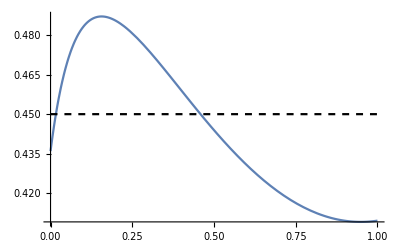

```mathematica
prs={d->15, n->4, μ->0.02, δ->0.005,p->0.45,b->15,c->1};
Show[Plot[EXDBde/.prs,{m,0,1}],ListPlot[{{0,p/.prs},{1, p/.prs}}, Joined->True,PlotStyle->{Black, Dashed}]]
```

### Moran Birth - Death

```mathematica
EXBDde=EXBD/.{Ieself->Idself,g->m}/.Idself->0//FullSimplify
```

(p ((b-c) (-1+p) δ μ (m-n+μ-m μ)-d^2 n (-c m (m-n) (-1+p) δ+μ+(m (-2+n)+(2 b (-1+m)^2+c (-2+m (2+m-2 n)+n)) (-1+p) δ) μ-(-1+m) (-2+n+(b (-1+m)-c (-2+n)) (-1+p) δ) μ^2)+d (m (m-n) (1+(b-c) (-1+p) δ)+(n+m (-2 m+n)+(b (m (-2+m-2 n)+3 n)+c (m (2+m)-(3+m) n+n^2)) (-1+p) δ) μ+(m^2-2 n+n^2-(b (-1+m) (-1+m-n)+c (-1+2 m+(-2+n) n)) (-1+p) δ) μ^2)))/(d (m^2 (-1+μ)^2-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ)))

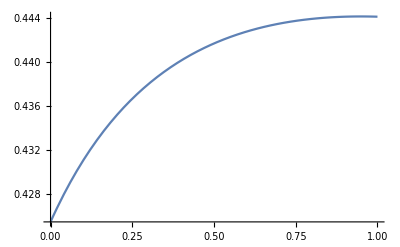

```mathematica
prs={d->15, n->4, μ->0.2, δ->0.005,p->0.45,b->15,c->1};
Show[Plot[EXBDde/.prs,{m,0,1}],ListPlot[{{0,p/.prs},{1, p/.prs}}, Joined->True,PlotStyle->{Black, Dashed}]]
```

### Moran Wright-Fisher

```mathematica
EXWFde=EXWF/.{Ieself->Idself,g->m}/.Idself->0;
```

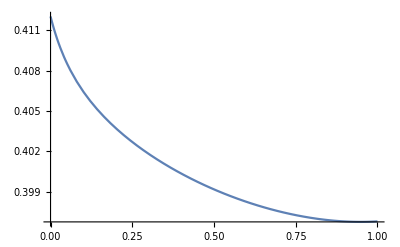

```mathematica
prs={d->15, n->4, μ->0.02, δ->0.005,p->0.45,b->15,c->1};
Show[Plot[EXWFde/.prs,{m,0,1}],ListPlot[{{0,p/.prs},{1, p/.prs}}, Joined->True,PlotStyle->{Black, Dashed}]]
```

## 5) Effect of deme size

### Moran Death - Birth

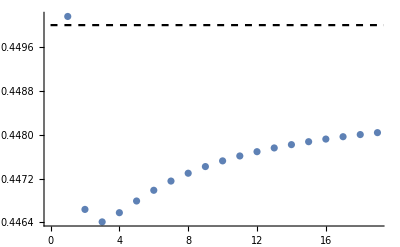

```mathematica
prs={d->15, μ->0.5, δ->0.005,p->0.45,b->15,c->1,m->0.01};
nmax = 20;
Show[ListPlot[Table[EXDB/.{Idself->0,Ieself->0,g->0}/.prs/.{n->nn},{nn,2,nmax}]],ListPlot[{{0,p/.prs},{nmax, p/.prs}}, Joined->True,PlotStyle->{Black, Dashed}]]
```